### Clean up. Build out of composites.

```mathematica
GraphicsRow/@Transpose[{CellularAutomatonHistoryPlot["GameOfLife",{CellularAutomaton["GameOfLife",{Reverse/@$LifeData[#]["MatrixData"],0},{{{6}}}],0},30,"Margin"-> 3]&/@{"Ecologist","Schick engine"},CellularAutomatonPlot3D["GameOfLife",{CellularAutomaton["GameOfLife",{Reverse/@$LifeData[#]["MatrixData"],0},{{{6}}}],0},60]&/@{"Ecologist","Schick engine"},CellularAutomatonSpacetimePlot["GameOfLife",{CellularAutomaton["GameOfLife",{Reverse/@$LifeData[#]["MatrixData"],0},{{{6}}}],0},60]&/@{"Ecologist","Schick engine"}}]
```

{-Graphics-,-Graphics-}

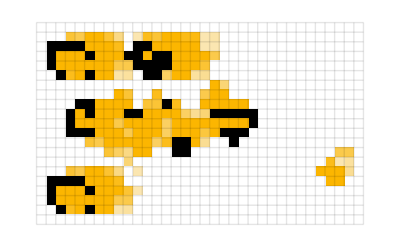
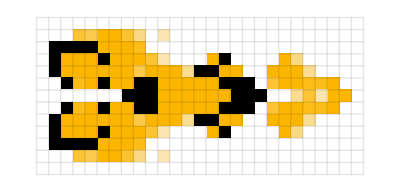
Ecologist | -Graphics- | -Graphics- | -Graphics3D- | -Graphics-
Schick engine | -Graphics- | -Graphics- | -Graphics3D- | -Graphics-

```mathematica
Grid[CellularAutomatonCompositePlot[#,{"Static"->{100, 100},{"Trails",10,.9}->{Automatic, 80},{"3D",60}->{100, 100},{"Spacetime", 60}->75}]&/@#,Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{1.5, 1.5}]&@ {"Ecologist","Schick engine"}
```

### Fix y scale labels have √□ symbols Annotate points by having them be little lines (usually vertical) Add back in colors

Work in progress, not sure if this is right, gives you an idea though

#### V2

Something is wrong here, and I can’t figure out what, I will come back to it

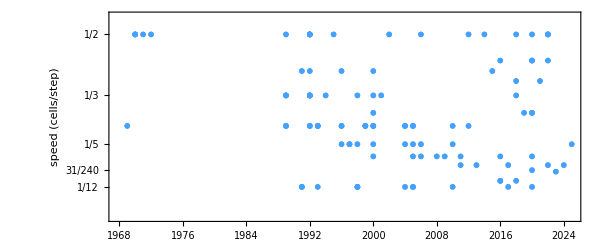

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[Tooltip[{#Year,Norm[#Speed]},If[Times@@Dimensions[#MatrixData]>5000, "Too large",CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, Min[5#Period, 100]]]]& ,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,InputForm[#]}&/@Union[Last/@data],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle-> RGBColor[0.27, 0.63, 1],PlotMarkers->({Graphics[#, PlotRange->{{-1, 1}, {-1, 1}}], 30}&/@as)]]
```

```mathematica
as =
Map[
If[Times@@Dimensions[#MatrixData]<10000, Line[{{0, 0}, #}]&[getvector[#]],Line[{{0, 0}, {0, 1}}]] &,Values[Select[$LifeData,#Class==="Spaceship"&]]];
```

```mathematica
hists  = CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, Min[5#Period, 100], "Decay"-> .9]&/@ Select[Values[Select[$LifeData,#Class==="Spaceship"&]], Times@@Dimensions[#MatrixData]<10000&];
```

```mathematica
smallas =
Map[
If[Times@@Dimensions[#MatrixData]<10000, Line[{{0, 0}, #}]&[getvector[#]],Line[{{0, 0}, {0, 1}}]] &,
Select[Values[Select[$LifeData,#Class==="Spaceship"&]], Times@@Dimensions[#MatrixData]<10000&]];
```

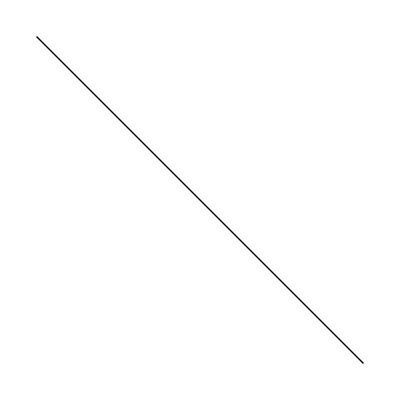
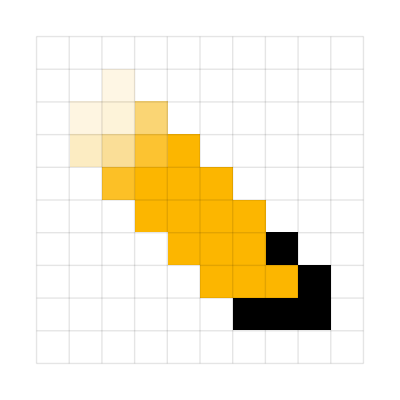
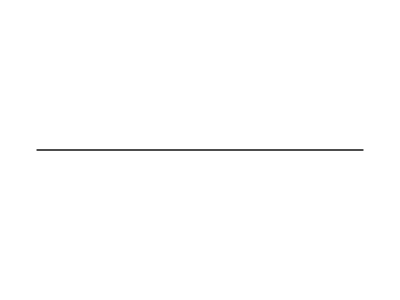
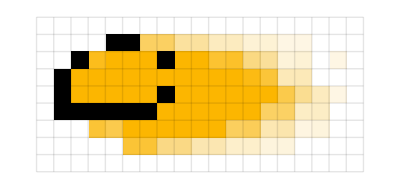
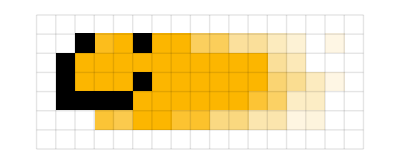
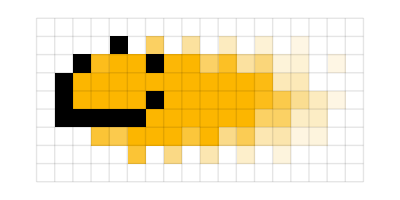
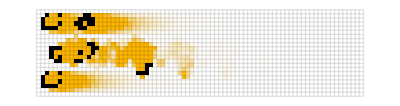
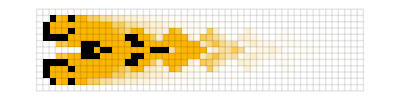
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Transpose[{Graphics/@as, hists}]
```

```mathematica
{Graphics[Arrow[{{0, 0}, #}]&[getvector[#]], PlotRange->{{-1,1}, {-1, 1}}], CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10#Period, "Decay"-> .9], #Speed}&/@Take[Values[Select[$LifeData,#Class==="Spaceship"&]], {60, 80}]
```

{{-Graphics-,-Graphics-,1/2},{-Graphics-,-Graphics-,1/5},{-Graphics-,-Graphics-,1/4},{-Graphics-,-Graphics-,1/12},{-Graphics-,-Graphics-,1/4},{-Graphics-,-Graphics-,1/4},{-Graphics-,-Graphics-,1/12},{-Graphics-,-Graphics-,1/12},{-Graphics-,-Graphics-,1/5},{-Graphics-,-Graphics-,1/4},{-Graphics-,-Graphics-,1/6},{-Graphics-,-Graphics-,1/6},{-Graphics-,-Graphics-,1/5},{-Graphics-,-Graphics-,1/2},{-Graphics-,-Graphics-,1/6},{-Graphics-,-Graphics-,1/6},{-Graphics-,-Graphics-,1/5},{-Graphics-,-Graphics-,1/12},{-Graphics-,-Graphics-,1/4},{-Graphics-,-Graphics-,1/6},{-Graphics-,-Graphics-,1/7}}

### Try to have spaceships go in the same direction [and/or show arrows]

Also requested to sort by direction in addition to period. Need to figure out how to prevent arrows from getting squished

For Developer

#### sorting by year and direction

```mathematica
bydirperiod = SortBy[(SortBy[#, #Year&]&/@ GatherBy[Values[Select[$LifeData, #Class==="Spaceship"&& KeyExistsQ[#, "Period"]&&2<#[["Period"]]<60&]], {#Period, getvector[#]}&]), #[[1, "Period"]]&];
```

```mathematica
Row[Column[Labeled[Column[{GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0, 0},ImageSize->2 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top ]&/@#],NumberLinePlot[Callout[#Year,#Year]&/@#,Axes->None,PlotRange->{1968,2025}]}],
Graphics[{Arrow[{{0, 0}, getvector[#[[1]]]}], Style[Text["period "<>ToString[#[[1, "Period"]]]<>"  ",  {-3, 0}], 12]}, PlotRange->{{-6, 2}, {-3, 3}}, ImageSize->{75, Automatic}, PlotRangePadding->0],Left]&/@ (im = DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#), Dividers->{None,GrayLevel[.8]}]&/@{bydirperiod[[;;11]],bydirperiod[[12;;20]]}, Spacer[15]]
```

-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-

#### All downward by period

```mathematica
byperiod = SortBy[#, #Year&]&/@SortBy[GatherBy[Values[Select[$LifeData, #Class==="Spaceship"&& KeyExistsQ[#, "Period"]&&2<=#[["Period"]]<60&]], #Period&], #[[1, "Period"]]&];
```

```mathematica
Row[Column[Labeled[Column[{GraphicsRow[
Labeled[Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},3#Period,PlotRangePadding->{0, 0},ImageSize->2 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]], getangle[getvector[#]]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top ]&/@#],NumberLinePlot[Callout[#Year,#Year]&/@#,Axes->None,PlotRange->{1968,2025}]}],
Text["period "<>ToString[#[[1, "Period"]]]<>"  "],Left]&/@ (DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#), Dividers->{None,GrayLevel[.8]}]&/@{byperiod[[;;10]],byperiod[[11;;]]}, Spacer[15]]
```

-Graphics-
-Graphics-period 2  
-Graphics-
-Graphics-period 3  
-Graphics-
-Graphics-period 4  
-Graphics-
-Graphics-period 5  
-Graphics-
-Graphics-period 6  
-Graphics-
-Graphics-period 7  
-Graphics-
-Graphics-period 8  
-Graphics-
-Graphics-period 9  
-Graphics-
-Graphics-period 10  
-Graphics-
-Graphics-period 12  -Graphics-
-Graphics-period 15  
-Graphics-
-Graphics-period 16  
-Graphics-
-Graphics-period 20  
-Graphics-
-Graphics-period 21  
-Graphics-
-Graphics-period 30  
-Graphics-
-Graphics-period 36

#### All downward by direction and period

```mathematica
bydirperiod = SortBy[(SortBy[#, #Year&]&/@ GatherBy[Values[Select[$LifeData, #Class==="Spaceship"&& KeyExistsQ[#, "Period"]&&2<=#[["Period"]]<60&]], {#Period, getvector[#]}&]), #[[1, "Period"]]&];
```

```mathematica
Row[Column[Labeled[Column[{GraphicsRow[
Labeled[Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},3#Period,PlotRangePadding->{0, 0},ImageSize->2 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]], getangle[getvector[#]]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top ]&/@#],NumberLinePlot[Callout[#Year,#Year]&/@#,Axes->None,PlotRange->{1968,2025}]}],
Graphics[{Arrow[{{0, 0}, getvector[#[[1]]]}], Style[Text["period "<>ToString[#[[1, "Period"]]]<>"  ",  {-3, 0}], 12]}, PlotRange->{{-6, 2}, {-3, 3}}, ImageSize->{75, Automatic}, PlotRangePadding->0],Left]&/@ (DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#), Dividers->{None,GrayLevel[.8]}]&/@{bydirperiod[[;;11]],bydirperiod[[12;;20]]}]
```

-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-

#### All downward by direction only

```mathematica
bydir = SortBy[(SortBy[#, #Year&]&/@ GatherBy[Values[Select[$LifeData, #Class==="Spaceship"&& KeyExistsQ[#, "Period"]&&2<#[["Period"]]<60&]], Sign[getvector[#]]&]), #[[1, "Period"]]&];
```

```mathematica
directions = <|{-1, 0}-> "left", {1, 0}-> "right", {0, 1}-> "up", {0, -1}-> "down", {-1, 1}-> "topleft", {1, 1}-> "bottomleft", {1, -1}-> "bottomright", {-1, -1}-> "bottomright"|>;
```

All:

```mathematica
Map[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0, 0},ImageSize->2 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]],Text[Style[#Year,9,GrayLevel[.3]]]]&, bydir, {2}]
```

{{-Graphics-1989,-Graphics-1989,-Graphics-1991,-Graphics-1992,-Graphics-1992,-Graphics-1992,-Graphics-1992,-Graphics-1992,-Graphics-1992,-Graphics-1992,-Graphics-1994,-Graphics-1996,-Graphics-1996,-Graphics-1997,-Graphics-1997,-Graphics-1998,-Graphics-1998,-Graphics-2000,-Graphics-2000,-Graphics-2000,-Graphics-2001,-Graphics-2004,-Graphics-2006,-Graphics-2008,-Graphics-2009,-Graphics-2010,-Graphics-2012,-Graphics-2012,-Graphics-2014,-Graphics-2015,-Graphics-2016,-Graphics-2016,-Graphics-2016,-Graphics-2016,-Graphics-2017,-Graphics-2018,-Graphics-2019,-Graphics-2020,-Graphics-2020,-Graphics-2020,-Graphics-2020,-Graphics-2020,-Graphics-2022,-Graphics-2022,-Graphics-2022,-Graphics-2022,-Graphics-2024,-Graphics-2025},{-Graphics-1969},{-Graphics-1970,-Graphics-1970,-Graphics-1970,-Graphics-1971,-Graphics-1972,-Graphics-1989,-Graphics-1989,-Graphics-1992,-Graphics-1992,-Graphics-1992,-Graphics-1992,-Graphics-1992,-Graphics-1992,-Graphics-1992,-Graphics-1996,-Graphics-2000,-Graphics-2000,-Graphics-2002,-Graphics-2006,-Graphics-2013,-Graphics-2018,-Graphics-2020,-Graphics-2022},{-Graphics-1989,-Graphics-1993,-Graphics-1993,-Graphics-1993,-Graphics-1996,-Graphics-1999,-Graphics-1999,-Graphics-1999,-Graphics-2000,-Graphics-2000,-Graphics-2000,-Graphics-2004,-Graphics-2004,-Graphics-2005,-Graphics-2005,-Graphics-2005,-Graphics-2005,-Graphics-2006,-Graphics-2010,-Graphics-2011,-Graphics-2011,-Graphics-2018,-Graphics-2021,-Graphics-2023},{-Graphics-1995,-Graphics-2018}}

Improvements

```mathematica
Row[Column[Labeled[Column[{GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0, 0},ImageSize->2 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top ]&/@#],NumberLinePlot[Callout[#Year,#Year]&/@#,Axes->None,PlotRange->{1968,2025}]}],
Text[Lookup[directions, {Sign[getvector[#[[1]]]]}, "other"][[1]]],Left]&/@ (im = DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#), Dividers->{None,GrayLevel[.8]}]&/@{bydir}, Spacer[15]]
```

-Graphics-
-Graphics-up
-Graphics-
-Graphics-bottomright
-Graphics-
-Graphics-left
-Graphics-
-Graphics-topleft
-Graphics-
-Graphics-right

#### By velocity

```mathematica
byspeed = SortBy[(SortBy[#, #Year&]&/@ GatherBy[Values[Select[$LifeData, #Class==="Spaceship"&& KeyExistsQ[#, "Period"]&&2<#[["Period"]]<60&]], Sign[getvector[#]]&]), #[[1, "Period"]]&];
```

#### By speed

```mathematica
$LifeData["Sir robin's knightship"]
```

### Getting arrows right

```mathematica
Length/@ bydirperiod
```

{1,2,9,1,2,4,10,14,1,2,4,5,1,1,2,2,2,4,1,1,3,3,4,1,1,1,1,2,1,3,1,1,1,1,1,1,1,1,1}

```mathematica
Labeled[GraphicsRow[
Labeled[Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0, 0},ImageSize->6Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]]^.8,Mesh->True,MeshStyle->Opacity[.1]], getangle[getvector[#]]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top ]&/@#], Column[{Text["period "<>ToString[#[[1, "Period"]]]<>"  "], Row[getvector[#[[1]]]]}],Left]&/@ (DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#)&[bydirperiod]
```

{-Graphics-period 3  
1/30,-Graphics-period 3  
-1/30,-Graphics-period 3  
01/3,-Graphics-period 4  
1/4-1/4,-Graphics-period 4  
01/4,-Graphics-period 4  
-1/40,-Graphics-period 4  
-1/20,-Graphics-period 4  
-1/41/4,-Graphics-period 5  
-1/50,-Graphics-period 5  
01/5,-Graphics-period 5  
-1/51/5,-Graphics-period 5  
02/5,-Graphics-period 6  
01/3,-Graphics-period 6  
01/2,-Graphics-period 6  
-1/60,-Graphics-period 6  
-1/61/6,-Graphics-period 6  
-1/61/3,-Graphics-period 6  
01/6,-Graphics-period 7  
-1/70,-Graphics-period 7  
-1/71/7,-Graphics-period 7  
01/7,-Graphics-period 7  
02/7,-Graphics-period 7  
03/7,-Graphics-period 8  
-1/20,-Graphics-period 8  
01/2,-Graphics-period 8  
01/4,-Graphics-period 8  
-1/81/8,-Graphics-period 9  
01/3,-Graphics-period 10  
01/5,-Graphics-period 10  
01/10,-Graphics-period 12  
01/2,-Graphics-period 12  
-1/20,-Graphics-period 15  
01/5,-Graphics-period 16  
1/20,-Graphics-period 20  
-1/20,-Graphics-period 20  
01/2,-Graphics-period 21  
02/7,-Graphics-period 30  
01/5,-Graphics-period 36  
01/2}

```mathematica
Style[Row[Labeled[GraphicsRow[Labeled[Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0,0},ImageSize->18 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]]^.3,Mesh->True,MeshStyle->Opacity[.1]],getangle[getvector[#]]+Pi/2],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@#],Text[Style["period "<>ToString[#[[1,"Period"]]]<>"  ",10]],Left]&/@(DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#)&[bydirperiod],"|"],LineSpacing->{1,1}]
```

||-Graphics-period 3  -Graphics-period 3  -Graphics-period 3  -Graphics-period 4  -Graphics-period 4  -Graphics-period 4  -Graphics-period 4  -Graphics-period 4  -Graphics-period 5  -Graphics-period 5  -Graphics-period 5  -Graphics-period 5  -Graphics-period 6  -Graphics-period 6  -Graphics-period 6  -Graphics-period 6  -Graphics-period 6  -Graphics-period 6  -Graphics-period 7  -Graphics-period 7  -Graphics-period 7  -Graphics-period 7  -Graphics-period 7  -Graphics-period 8  -Graphics-period 8  -Graphics-period 8  -Graphics-period 8  -Graphics-period 9  -Graphics-period 10  -Graphics-period 10  -Graphics-period 12  -Graphics-period 12  -Graphics-period 15  -Graphics-period 16  -Graphics-period 20  -Graphics-period 20  -Graphics-period 21  -Graphics-period 30  -Graphics-period 36

```mathematica
bydirperiod = SortBy[(SortBy[#, #Year&]&/@ GatherBy[Values[Select[$LifeData, #Class==="Spaceship"&& KeyExistsQ[#, "Period"]&&2<=#[["Period"]]<60&]], {#Period, getvector[#]}&]), #[[1, "Period"]]&];
```

```mathematica
Style[Row[Labeled[GraphicsRow[Labeled[Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0,0},ImageSize->18 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]]^.3,Mesh->True,MeshStyle->Opacity[.05 ]],getangle[getvector[#]]+Pi/2],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@#],Column[{Text["period "<>ToString[#[[1, "Period"]]]<>"  "], getvector[#[[1]]]}],Left]&/@(DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#)&[bydirperiod],"|"],LineSpacing->{1,1}]
```

```mathematica
Graphics[{Arrow[{{0, 0}, getvector[#[[1]]]}], Style[Text["period "<>ToString[#[[1, "Period"]]]<>"  ",  {-3, 0}], 12]}, PlotRange->{{-6, 2}, {-3, 3}}, ImageSize->{75, Automatic}, PlotRangePadding->0]
```

||-Graphics-period 2  
{0,1/2}-Graphics-period 2  
{1/2,0}-Graphics-period 3  
{1/3,0}-Graphics-period 3  
{-1/3,0}-Graphics-period 3  
{0,1/3}-Graphics-period 4  
{1/4,-1/4}-Graphics-period 4  
{0,1/4}-Graphics-period 4  
{-1/4,0}-Graphics-period 4  
{-1/2,0}-Graphics-period 4  
{-1/4,1/4}-Graphics-period 5  
{-1/5,0}-Graphics-period 5  
{0,1/5}-Graphics-period 5  
{-1/5,1/5}-Graphics-period 5  
{0,2/5}-Graphics-period 6  
{0,1/3}-Graphics-period 6  
{0,1/2}-Graphics-period 6  
{-1/6,0}-Graphics-period 6  
{-1/6,1/6}-Graphics-period 6  
{-1/6,1/3}-Graphics-period 6  
{0,1/6}-Graphics-period 7  
{-1/7,0}-Graphics-period 7  
{-1/7,1/7}-Graphics-period 7  
{0,1/7}-Graphics-period 7  
{0,2/7}-Graphics-period 7  
{0,3/7}-Graphics-period 8  
{-1/2,0}-Graphics-period 8  
{0,1/2}-Graphics-period 8  
{0,1/4}-Graphics-period 8  
{-1/8,1/8}-Graphics-period 9  
{0,1/3}-Graphics-period 10  
{0,1/5}-Graphics-period 10  
{0,1/10}-Graphics-period 12  
{0,1/2}-Graphics-period 12  
{-1/2,0}-Graphics-period 15  
{0,1/5}-Graphics-period 16  
{1/2,0}-Graphics-period 20  
{-1/2,0}-Graphics-period 20  
{0,1/2}-Graphics-period 21  
{0,2/7}-Graphics-period 30  
{0,1/5}-Graphics-period 36  
{0,1/2}

```mathematica
bydirperiod = SortBy[(SortBy[#, #Year&]&/@ GatherBy[Values[Select[$LifeData, #Class==="Spaceship"&& KeyExistsQ[#, "Period"]&&2<=#[["Period"]]<60&]], {#Period, Sort[Abs[getvector[#]]]}&]), #[[1, "Period"]]&];
```

```mathematica
Style[Row[Labeled[GraphicsRow[Labeled[Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0,0},ImageSize->18 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]]^.3,Mesh->True,MeshStyle->Opacity[.1]],With[{vec = getvector[#]},getangle[vec]+If[SameQ@@Abs[vec],0,  Pi/2]]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@#],Column[{Text["period "<>ToString[#[[1, "Period"]]]<>"  "], Rotate[Graphics[Text[Style["⟶",Bold,11],{0,0}]],
 getinitialangle[getvector[#[[1]]]]]}],Left]&/@(DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#)&[bydirperiod],"|"],LineSpacing->{1,1}]
```

||-Graphics-period 2  
-Graphics--Graphics-period 3  
-Graphics--Graphics-period 4  
-Graphics--Graphics-period 4  
-Graphics--Graphics-period 4  
-Graphics--Graphics-period 5  
-Graphics--Graphics-period 5  
-Graphics--Graphics-period 5  
-Graphics--Graphics-period 6  
-Graphics--Graphics-period 6  
-Graphics--Graphics-period 6  
-Graphics--Graphics-period 6  
-Graphics--Graphics-period 6  
-Graphics--Graphics-period 7  
-Graphics--Graphics-period 7  
-Graphics--Graphics-period 7  
-Graphics--Graphics-period 7  
-Graphics--Graphics-period 8  
-Graphics--Graphics-period 8  
-Graphics--Graphics-period 8  
-Graphics--Graphics-period 9  
-Graphics--Graphics-period 10  
-Graphics--Graphics-period 10  
-Graphics--Graphics-period 12  
-Graphics--Graphics-period 15  
-Graphics--Graphics-period 16  
-Graphics--Graphics-period 20  
-Graphics--Graphics-period 21  
-Graphics--Graphics-period 30  
-Graphics--Graphics-period 36  
-Graphics-

```mathematica
AngleVector[getinitialangle[{1/4, 1/4}]]
```

{1/(√2),-1/(√2)}

```mathematica
Style[Row[Labeled[GraphicsRow[Labeled[Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0,0},ImageSize->18 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]]^.3,Mesh->True,MeshStyle->Opacity[.1]],With[{vec = getvector[#]},getangle[vec]+If[SameQ@@Abs[vec],0,  Pi/2]]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@#],Column[{Text["period "<>ToString[#[[1, "Period"]]]<>"  "], Row[{Text["speed"],Style[Text[#[[1, "Speed"]]], 10],Rasterize[Graphics[{Arrowheads[.4],Thickness[.075], Arrow[{{0, 0}, {.9, 1}*AngleVector[getinitialangle[getvector[#[[1]]]]]}]}, PlotRange->{{-.1, 1.1}, {-1, .75}}, ImageSize->{20, Automatic}], RasterSize->100]}]}],Left]&/@(DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#)&[bydirperiod],"|"],LineSpacing->{1,1}]
```

||-Graphics-period 2  
speed1/2-Graphics--Graphics-period 3  
speed1/3-Graphics--Graphics-period 4  
speed1/4-Graphics--Graphics-period 4  
speed1/2-Graphics--Graphics-period 4  
speed1/4-Graphics--Graphics-period 5  
speed1/5-Graphics--Graphics-period 5  
speed1/5-Graphics--Graphics-period 5  
speed2/5-Graphics--Graphics-period 6  
speed1/3-Graphics--Graphics-period 6  
speed1/2-Graphics--Graphics-period 6  
speed1/6-Graphics--Graphics-period 6  
speed{1/3,1/6}-Graphics--Graphics-period 6  
speed1/6-Graphics--Graphics-period 7  
speed1/7-Graphics--Graphics-period 7  
speed2/7-Graphics--Graphics-period 7  
speed1/7-Graphics--Graphics-period 7  
speed3/7-Graphics--Graphics-period 8  
speed1/4-Graphics--Graphics-period 8  
speed1/8-Graphics--Graphics-period 8  
speed1/2-Graphics--Graphics-period 9  
speed1/3-Graphics--Graphics-period 10  
speed1/5-Graphics--Graphics-period 10  
speed1/10-Graphics--Graphics-period 12  
speed1/2-Graphics--Graphics-period 15  
speed1/5-Graphics--Graphics-period 16  
speed1/2-Graphics--Graphics-period 20  
speed1/2-Graphics--Graphics-period 21  
speed2/7-Graphics--Graphics-period 30  
speed1/5-Graphics--Graphics-period 36  
speed1/2-Graphics-